# Combine Plots

## LEP experiment 1996

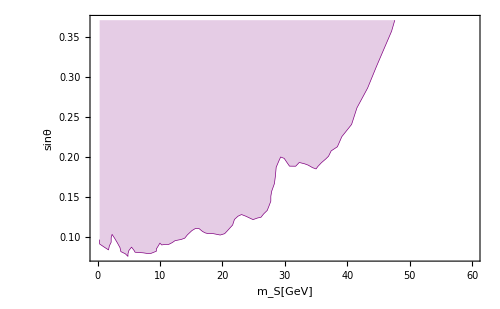

```mathematica
LEP1996data={#1,√#2}&@@@Import[NotebookDirectory[]<>"/probe/LEP1996.csv"];
LEP1996=ListLinePlot[LEP1996data,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Purple,Thickness[0.001]]]
```

## LHCb experiment

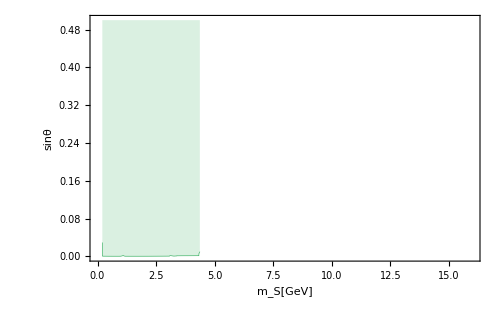

```mathematica
LHCbdata={#1, √#2}& @@@Import[NotebookDirectory[]<>"probe/LHCb.csv"];
LHCb=ListLinePlot[LHCbdata,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[ColorData[97,15],Thickness[0.001]],PlotRange->{{0,16},{0,0.5}}]
```

## Kaon decay

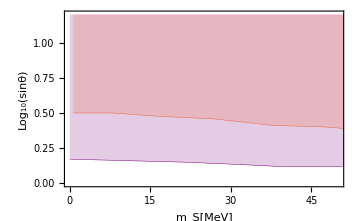

```mathematica
NA621={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-1.csv"];
NA622={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-2.csv"];
NA623={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-3.csv"];
E9491={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/E949.csv"];
E9492={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/E949-2.csv"];
Kaondecay=ListLinePlot[{NA621,E9491},Filling->Top,PlotRange->{{0,50},{0,1.2}},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["Log_10(sinθ)",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{Directive[Purple,Thickness[0.001]],Directive[ColorData[97,4],Thickness[0.001]]}]
```

## CMB probe

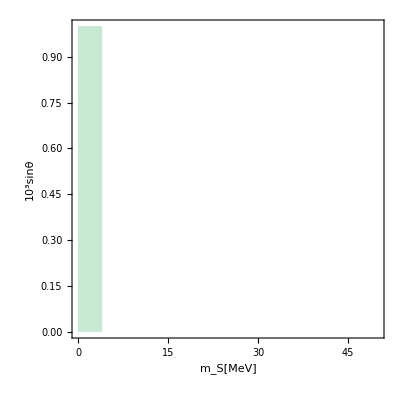

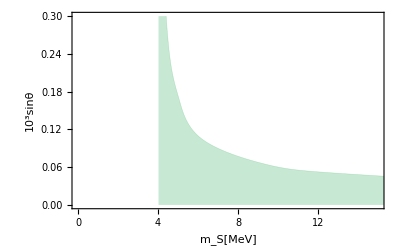

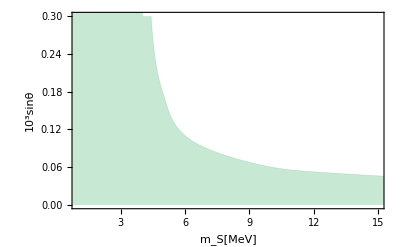

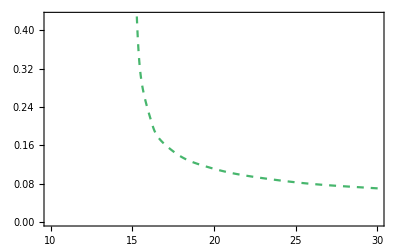

```mathematica
Planckdata={#1,1000#2}&@@@Import[NotebookDirectory[]<>"./probe/Planck.csv"];
CMBS4data=Import[NotebookDirectory[]<>"./probe/CMB-S4.csv"];
Planckfunc[mS_]:=Interpolation[Planckdata][mS]
CMBfunc[mS_]:=Interpolation[CMBS4data][mS]
perspect‵CMB‵data=SortBy[{#1,1000#2}&@@@Import[NotebookDirectory[]<>"./probe/CMB-perspective.csv"],First];
Planck01=RegionPlot[mS<=Min[{#1}&@@@Planckdata+0.015],{mS,0,50},{s,0,1.},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,PlotStyle->{ColorData[97,15],Opacity[0.3]}]//CleanRegionPlot
Planck02=ListLinePlot[Planckdata,PlotRange->{{0,15},{0,0.3}},InterpolationOrder->3,AxesOrigin->{1,0.},Filling->Bottom,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,PlotStyle->{ColorData[97,15],Opacity[0.3],Thickness[0.001]},FillingStyle->Opacity[0.3]]
Planck=Show[Planck02,Planck01,PlotRange->{{1,15},{0,0.3}}]
CMB‵perspect=ListLinePlot[perspect‵CMB‵data,InterpolationOrder->3,PlotRange->{{10,30},Automatic},PlotStyle->Directive[Dashed,ColorData[97,15]]]
```

## Supernovae

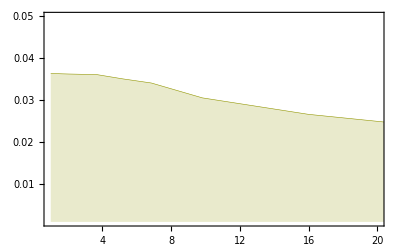

```mathematica
SNdata={#1,1000*#2}&@@@Import[NotebookDirectory[]<>"probe/SN.csv"];
SN=ListLinePlot[SNdata,Filling->Bottom,PlotStyle->{Directive[Thickness[0.001],ColorData[97,10]]},PlotRange->{{1,20},{0.001,0.05}}]
```

## SFOPT bound

### GeV scale

```mathematica
c100‵δ2pi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c100_delta_2pi5_GeV_out.csv"];
c100‵δ2pi5‵strength‵data={#1,#2,#10}&@@@c100‵δ2pi5‵data;
c30‵δ2pi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_2pi5_GeV_out.csv"];
c30‵δ2pi5‵strength‵data={#1,#2,#10}&@@@c30‵δ2pi5‵data;
c3‵δ2pi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_2pi5_GeV_out.csv"];
c3‵δ2pi5‵strength‵data={#1,#2,#10}&@@@Select[c3‵δ2pi5‵data,Length[#]>10 &];
c30‵δpi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_pi5_GeV_out.csv"];
c30‵δpi5‵strength‵data={#1,#2,1.2*#8}&@@@c30‵δpi5‵data;
c3‵δpi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_pi5_GeV_out.csv"];
c3‵δpi5‵strength‵data={#1,#2,1.2*#8}&@@@c3‵δpi5‵data;
```

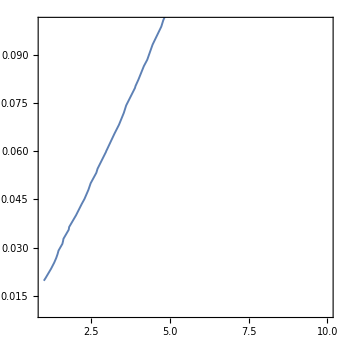

```mathematica
c100‵δ2pi5‵strength‵plot=ListContourPlot[c100‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->{{1,10},{0.01,0.1}},ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]]]
```

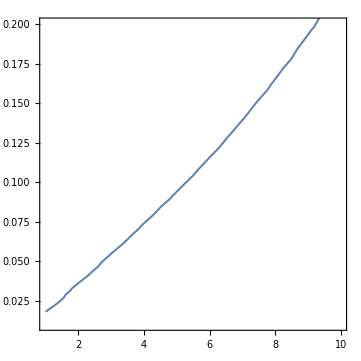

```mathematica
c30‵δ2pi5‵strength‵plot=ListContourPlot[c30‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->{{1,10},{0.01,0.2}},ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]]]
```

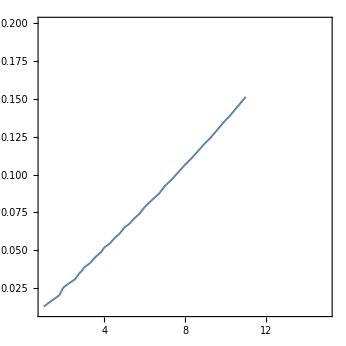

```mathematica
c3‵δ2pi5‵strength‵plot=ListContourPlot[c3‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->{{1,15},{0.01,0.2}},ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]]]
```

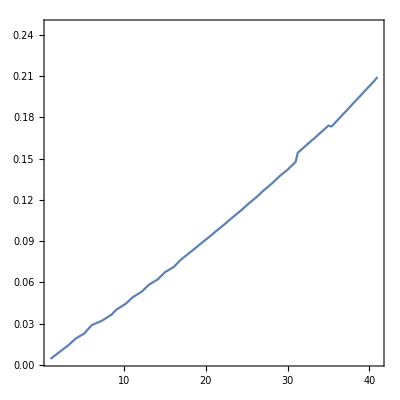

```mathematica
c3‵δpi5‵strength‵plot=ListContourPlot[c3‵δpi5‵strength‵data,Contours->{1.0},ContourShading->None,ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]],PlotRange->Full]
```

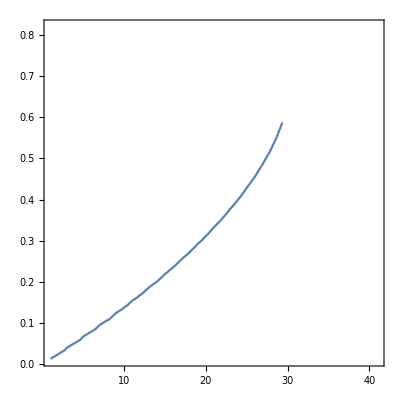

```mathematica
c30‵δpi5‵strength‵plot=ListContourPlot[c30‵δpi5‵strength‵data,Contours->{1.0},ContourShading->None,ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]],PlotRange->Full]
```

```mathematica
TnTcratiodata={#10/#8}&@@@Select[Select[c3‵δ2pi5‵data,(Length[#]>10 )&],1.3>#[[10]]>0.8 &]//Flatten;
```

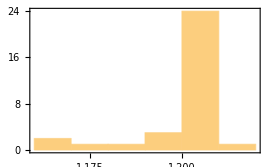

```mathematica
Histogram[TnTcratiodata]
```

```mathematica
Mean[TnTcratiodata]
```

1.20016

## MeV

```mathematica
c100‵δ2pi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c100_delta_2pi5_MeV_out.csv"];
c100‵δ2pi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c100‵δ2pi5‵MeV‵data;
c30‵δ2pi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_2pi5_MeV_out.csv"];
c30‵δ2pi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c30‵δ2pi5‵MeV‵data;
c3‵δ2pi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_2pi5_MeV_out.csv"];
c3‵δ2pi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c3‵δ2pi5‵MeV‵data;
c3‵δpi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_pi5_MeV_out.csv"];
c3‵δpi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c3‵δpi5‵MeV‵data;
c30‵δpi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_pi5_MeV_out.csv"];
c30‵δpi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c30‵δpi5‵MeV‵data;
```

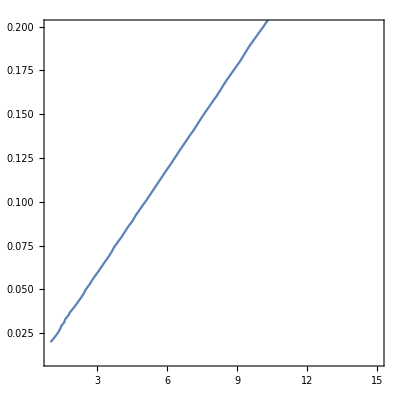

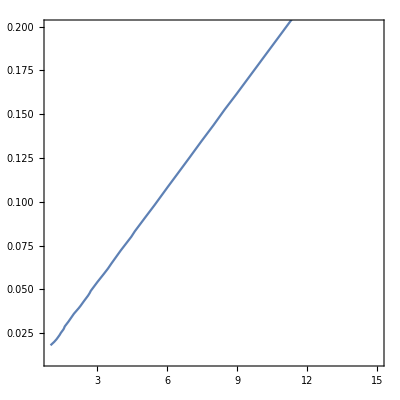

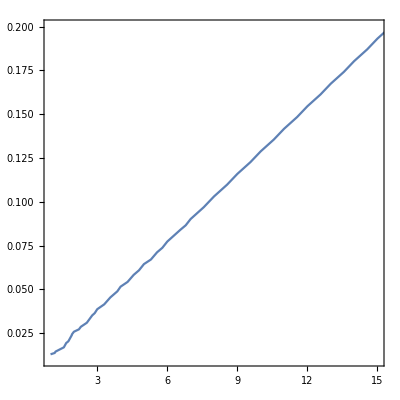

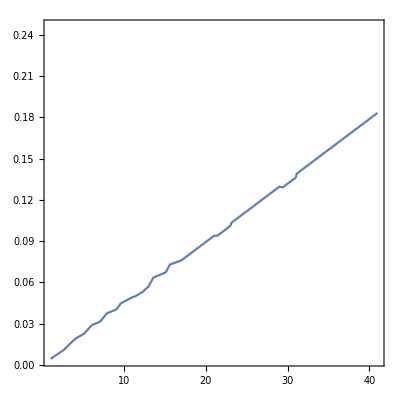

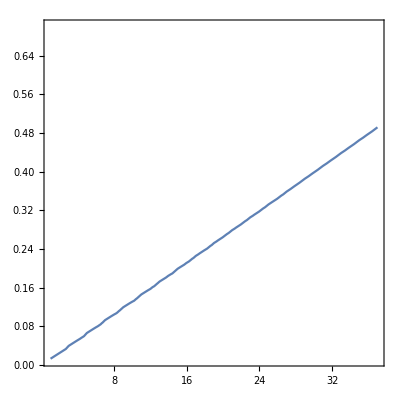

```mathematica
c100‵δ2pi5‵MeV‵strength‵plot=ListContourPlot[c100‵δ2pi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->{{1,15},{0.01,0.2}},ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]]]
c30‵δ2pi5‵MeV‵strength‵plot=ListContourPlot[c30‵δ2pi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->{{1,15},{0.01,0.2}},ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]]]
c3‵δ2pi5‵MeV‵strength‵plot=ListContourPlot[c3‵δ2pi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->{{1,15},{0.01,0.2}},ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]]]
c3‵δpi5‵MeV‵strength‵plot=ListContourPlot[c3‵δpi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]]]
c30‵δpi5‵MeV‵strength‵plot=ListContourPlot[c30‵δpi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,ContourStyle->Directive[Thickness[0.004],ColorData[97,1],Opacity[1]]]
```

## Combine

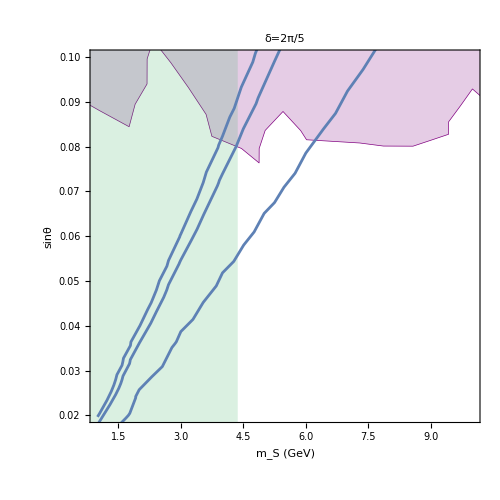

```mathematica
Show[LEP1996,LHCb,c100‵δ2pi5‵strength‵plot,c30‵δ2pi5‵strength‵plot,c3‵δ2pi5‵strength‵plot,PlotRange->{{1,10},{0.02,0.1}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->24],Style["sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=2π/5",FontFamily->"Times",FontSize->26]]
```

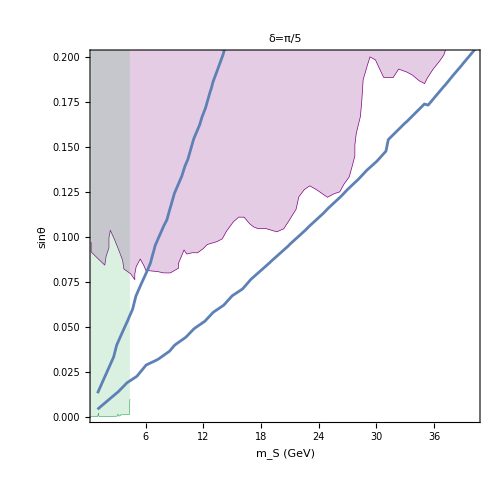

```mathematica
Show[LEP1996,LHCb,c3‵δpi5‵strength‵plot,c30‵δpi5‵strength‵plot,PlotRange->{{1,40},{0.001,0.2}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->24],Style["sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/5",FontFamily->"Times",FontSize->26]]
```

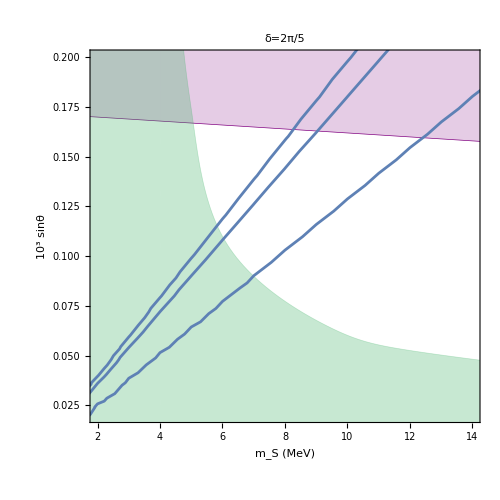

```mathematica
Show[Kaondecay,CMB‵perspect,Planck,c100‵δ2pi5‵MeV‵strength‵plot,c30‵δ2pi5‵MeV‵strength‵plot,c3‵δ2pi5‵MeV‵strength‵plot,PlotRange->{{2,14},{0.02,0.2}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (MeV)",FontFamily->"Times",FontSize->24],Style["10^3 sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=2π/5",FontFamily->"Times",FontSize->26]]
```

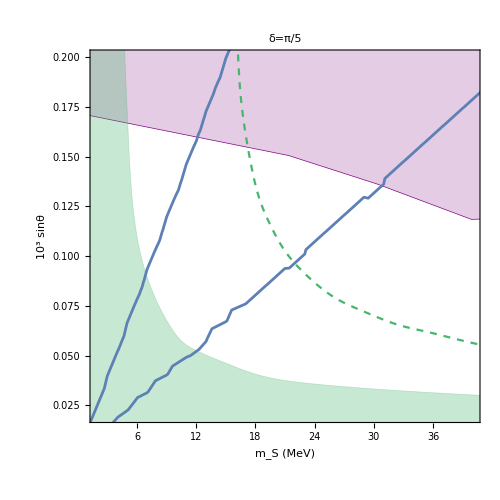

```mathematica
Show[Kaondecay,CMB‵perspect,Planck,c3‵δpi5‵MeV‵strength‵plot,c30‵δpi5‵MeV‵strength‵plot,PlotRange->{{2,40},{0.02,0.2}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (MeV)",FontFamily->"Times",FontSize->24],Style["10^3 sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/5",FontFamily->"Times",FontSize->26]]
```